Piecewise[{{32+12 x-2 x^2, x≤3.99515}, {64-ⅇ^(1/2-0.0313259 x^2) x^2, 3.99515<x}, {0, True}}]

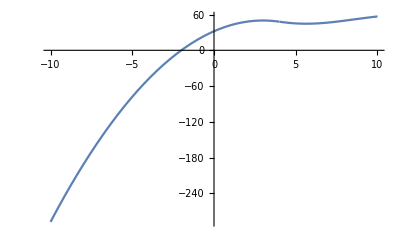

Definitionsbereich:

Reell:True

Komplex:True

Wertebereich:

Reell:y<64.

Piecewise[{{12.-4. x, 23265174 x<92947937}, {ⅇ^(-0.0313259 x^2) (-3.29744 x+0.103295 x^3), 23265174 x>92947937}, {Indeterminate, True}}]

Definitionsbereich:

Reell:x<92947937/23265174||x>92947937/23265174

Komplex:-92947937+23265174 x≠0

Wertebereich:

FunctionRange::nmet: Unable to find the range with the available methods.

Reell:FunctionRange[Piecewise[{{12.-4. x, 23265174 x<92947937}, {ⅇ^(-0.0313259 x^2) (-3.29744 x+0.103295 x^3), 23265174 x>92947937}, {Indeterminate, True}}],x,y]

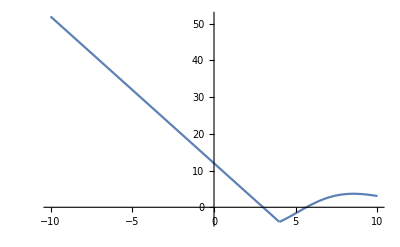

```mathematica
a=64;
b=5.65;
functionpart1 = -2x^2+12x+32;
definitionsbereich1 = (x≤(b/Sqrt[2]));
funktionspart2 =a-x^2E^(1/2-(x^2/b^2));
definitionsbereich2 = (b/Sqrt[2]<x);

func=Piecewise[{{functionpart1, definitionsbereich1},{  funktionspart2,definitionsbereich2}}]
Plot[func,{x,-10,10},PlotRange->All]

Print["Definitionsbereich:"]
Print["Reell:",FunctionDomain[func, x, Reals]]
Print["Komplex:",FunctionDomain[func, x, Complexes]]
Print["Wertebereich:"]
Print["Reell:",FunctionRange[func, x, y]]
ableitung = Simplify[D[func,x]]
Print["Definitionsbereich:"]
Print["Reell:",FunctionDomain[ableitung, x, Reals]]
Print["Komplex:",FunctionDomain[ableitung, x, Complexes]]
Print["Wertebereich:"]
Print["Reell:",FunctionRange[ableitung, x, y]]
Plot[ableitung, {x,-10,10}]
```